# Aula 09 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

Um método clássico para determinação de raízes de uma função de uma variável  𝒻(𝓍) é o método de Newton-Raphson, implementado através de mapeamento: x_(n +1) = x_n - f(x_n)/f ’(x_n). O método é bastante eficiente para encontrar um zero de 𝒻(𝓍) a partir de um palpite inicial x_0, desde que a aplicação repetida do mapeamento não produza valores de 𝓍 próximos de um zero de 𝒻 ’(𝓍).[Observe a expressão de mapeamento para entender o motivo da falha do método nesse caso. Além disso, é claro que se tanto 𝒻(x^*) quanto 𝒻 ’(x^*) forem nulas em x = x^* o método não funcionará.]

## 1.

A função de Bessel J_0 (x) é invocada no Mathematica como BesselJ[0,x]. Produza um gráfico de J_0(x) com 𝓍 entre 0 e 20.

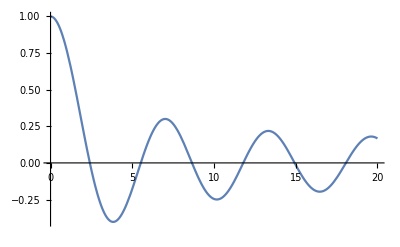

```mathematica
j0[x_]:= BesselJ[0,x]
Plot[j0[x],{x,0,20}]
```

## 2.

Utilizando funções puras e FixedPoint (ou seja, sem utilizar FindRoot), determine os zeros de J_0(x) contidos no intervalo 0< x < 20.
Respostas: 2.40483,5.52008,8.65373,11.7915,14.9309,18.0711

Vou me aproximar das 6 raízes da função de Bessel utilizando o gráfico pra me orientar nos chutes dos valores iniciais.

```mathematica
(*Devido a um erro na hora de calular, calularemos a derivada da função de Bessel e usaremos apenas o seu resultado no método de Newton- Raphson*)
D[BesselJ[0,x],x]
```

-BesselJ[1,x]

```mathematica
chutes = {2., 5., 9., 12., 15., 18.};
Do[Print[FixedPoint[Function[x,x-BesselJ[0,x]/(-BesselJ[1,x])],i]], {i,chutes}]
```

2.40483

5.52008

8.65373

11.7915

14.9309

18.0711